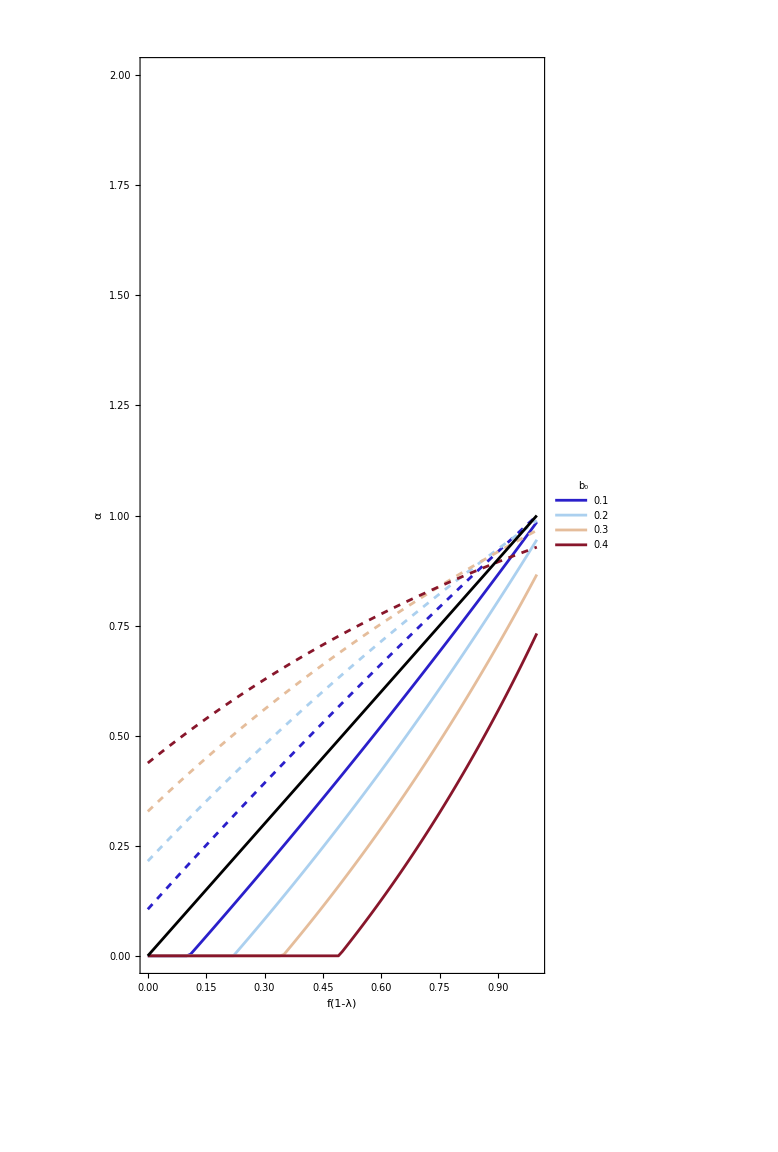

```mathematica
(*Define function to find 'x' where H=0 at the toe for given α,f,b0*)
xPosRoot[αv_?NumericQ,fv_?NumericQ, b0_?NumericQ,k_?NumericQ]:=Module[{sol,res},sol=Quiet@Check[NDSolve[{-D[H[x],x] - 0.5*(αv-2 b0 x)/(1+(2 b0 x)^2)*2 b0/(1+2 b0 x*αv)*H[x] == fv+2 b0 x -(αv-2 b0 x)/(1+2 b0 x*αv),H[0]==k*Abs[b0]},H,{x,0,1}],$Failed];
If[sol===$Failed,1.0,(*fallback if solve fails*)
Quiet@Check[res=x/.Last[FindRoot[((H[x]/. sol)==0),{x,0.9,0,1}]],0]
]
]
(*Define function to find 'x' where H=0 at the head for given α,f,b0*)
xNegRoot[αv_?NumericQ,fv_?NumericQ, b0_?NumericQ,k_?NumericQ]:=Module[{sol,res},sol=Quiet@Check[NDSolve[{-D[H[x],x] - 0.5*(αv-2 b0 x)/(1+(2 b0 x)^2)*2 b0/(1+2 b0 x*αv)*H[x] == fv+2 b0 x -(αv-2 b0 x)/(1+2 b0 x*αv),H[0]==k*Abs[b0]},H,{x,-1,0}],$Failed];
If[sol===$Failed,-1.0,(*fallback if solve fails*)
Quiet@Check[res=x/.Last[FindRoot[((H[x]/. sol)==0),{x,-0.9,-1,0}]],0]
]
]
(*Define functions to compute locus of stability*)
kval=3;
locusPosFun[f_?NumericQ,b0_?NumericQ,k_?NumericQ]:=Module[{res},res=
Quiet@FindRoot[xPosRoot[αsol,f,b0,k]==0.99,{αsol,0.0,0,10}];
αsol/. res]
locusNegFun[f_,b0_,k_]:=Module[{res},res=
Quiet@FindRoot[xNegRoot[αsol,f,b0,k]==-0.99,{αsol,1.2,0,10}];
αsol/. res]
bvals=Subdivide[0.1,0.4,3];
roundedLabels = Round[bvals,0.01];
fvals=Range[0,1,0.01];  

(*fv=1.0;
b0v=0.2;
αsol=locusPosFun[fv,b0v,kval]
xPosRoot[αsol,fv,b0v,kval]
αsol=locusNegFun[fv,b0v,kval]
(*xNegRoot[0.2,fv,b0v,kval]*)
xNegRoot[αsol,fv,b0v,kval]*)
bestα[b0_,k_] := Sqrt[(k*b0 - 2*b0)/b0/(2+k/2*b0^2)]
bestf[b0_,k_] := bestα[b0,k]*(1-k*b0^2)

(*Parallel computation of {f,alpha} pairs for each ρ,b value*)
dataPos=ParallelTable[{f,locusPosFun[f,b,kval]},{b,bvals},{f,fvals}];
dataNeg=ParallelTable[{f,locusNegFun[f,b,kval]},{b,bvals},{f,fvals}];
(*Plot each set of points as a line*)
p1=ListLinePlot[dataPos,PlotRange->{0,2},
PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,20]],Right],
LabelStyle->{FontSize->20},
ImageSize->Large,PlotStyle->ColorData["ThermometerColors"]/@Rescale[Range[Length[bvals]]]];
styles=Table[{ColorData["ThermometerColors"][r],Dashed},{r,Rescale[Range[Length[bvals]]]}];
p2=ListLinePlot[dataNeg,PlotRange->{0,2},
ImageSize->Large,
PlotStyle->styles];
data=Table[{bestf[b,kval],bestα[b,kval]},{b,bvals}];
p3=ListPlot[data,PlotStyle->{Red,PointSize[Large]},PlotRange->All,GridLines->Automatic];
p4=Plot[f,{f,0,1},PlotStyle->{Black}];
fig=Show[p1,p2,p4,FrameLabel->{"f(1-λ)","α"},Frame->True,LabelStyle->{FontSize->25},AspectRatio->2]
```